0.0544537

0.0770092

0.0943166

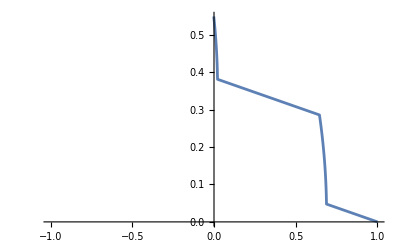

$Aborted

$Aborted

$Aborted

«6 more identical outputs»

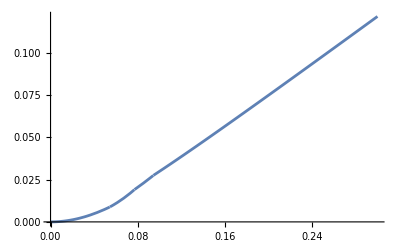

```mathematica
Clear["Global`*"]
hf=2.;hm=4.;c=10.;σf=200.;σB=1.;σT=10.; 
ϵD1=0.5;ϵD2=0.5;ϵD3=0.5;L=1000;
B=500;
α=hm/(2×hf);
β=B/L;
k=1;
Φ=1.5;
λ=1.4;
tanφ=√(3+β^2)−β;
cotφ=1/tanφ;
h=(hf+2×hm)/(4×c);
ρf=2.7×10^(-9);
C0=c/L;
σ5=(σT+σB)×0.5;
σ=σ5/σf;
σ1[A_]:=σB/(1-ϵ1[A])+(z-hf)/(c×(1-ϵ1[A])^2)×(σT-σB);
σ2[A_]:=σB/(1-ϵ2[A])+(z-hf-c×(1-ϵ1[A])-hm)/(c×(1-ϵ2[A])^2)×(σT-σB);
σ3[A_]:=σB/(1-ϵ3[A])+(z-hf-c×(1-ϵ1[A])-2×hm-c×(1-ϵ2[A]))/(c×(1-ϵ3[A])^2)×(σT-σB);
σa=σB+(z-hf)/c×(σT-σB);
ρd=(ρf×∫_hf^(hf+c) (σa/(k×σf))^(1/Φ)ⅆz)/c;
μ=2×ρf×(hf+hm)+3×ρd×c;
ρ=ρd/ρf;
A1=√((8×h×σ×ϵD1)/((4×h+3×ρ)×(3×ρ×(1+4×α)+8×h×(1+2×α))))
A2=√((8×h×σ×(ϵD1+ϵD2))/((4×h+3×ρ)×(3×ρ×(1+4×α)+8×h×(1+2×α))))
A3=√((8×h×σ×(ϵD1+ϵD2+ϵD3))/((4×h+3×ρ)×(3×ρ×(1+4×α)+8×h×(1+2×α))))
ϵ1[A_]:=Piecewise[{{((4×h+3×ρ)×(3×ρ×(1+4×α)+8×h×(1+2×α))×A^2)/(8×h×σ),0⩽A⩽A1},{ϵD1,A⩾A1}}];
ϵ2[A_]:=Piecewise[{{0,0⩽A⩽A1},{((4×h+3×ρ)×(3×ρ×(1+4×α)+8×h×(1+2×α))×A^2)/(8×h×σ)-ϵD1,A1⩽A⩽A2},{ϵD2,A⩾A2}}];
ϵ3[A_]:=Piecewise[{{0,0≤A⩽A1},{0,A1⩽A⩽A2},{((4×h+3×ρ)×(3×ρ×(1+4×α)+8×h×(1+2×α))×A^2)/(8×h×σ)-ϵD1-ϵD2,A2⩽A⩽A3},{ϵD3,A⩾A3}}];
NP1=2×σf×(hf+hm)+1.5×(σB+σT)×c;
H=2×(hf+hm)+3×c;
H1[A_]:=H-c×(ϵ1[A]+ϵ2[A]+ϵ3[A]);
MP[A_]:=-1/(6 (σB-σT)^2)(c (-6×hm+c (-8+2×ϵ1[A]+5×ϵ2[A]+ϵ3[A]))×σB^3-3×σB×σT×(-4×hf^2×σf-4×hm^2×σf+4×hf×(-2×hm+c×(-3+ϵ1[A]+ϵ2[A]+ϵ3[A]))×σf+2×c×hm×(2×(-1+ϵ2[A])×σf-σT)+c^2 (-2+ϵ2[A]+ϵ3[A])×σT)+σB^2 (-6×hf^2×σf-6×hm^2×σf+6×hf×(-2×hm+c×(-3+ϵ1[A]+ϵ2[A]+ϵ3[A]))×σf+6×c×hm×((-1+ϵ2[A])×σf+σT)+c^2×(-3×(-2+ϵ1[A]+ϵ2[A])×σT+√2 ×√((-1+ϵ2[A])^2 (σB^2+σT^2))))+σT^2×(-6×hf^2×σf-6×hm^2×σf+6×hf×(-2×hm+c×(-3+ϵ1[A]+ϵ2[A]+ϵ3[A]))×σf+6×c×hm×((-1+ϵ2[A]) ×σf-σT)+c^2×((-8+ϵ1[A]+5 ϵ2[A]+2 ϵ3[A])×σT+√2×√((-1+ϵ2[A])^2 (σB^2+σT^2)))));
zp[A_]:=1/(2 (σB/c-σT/c))(4 σB+(2 hf σB)/c+(2 hm σB)/c-2 ϵ1[A] σB-2 ϵ2[A] σB-2 σT-(2 hf σT)/c-(2 hm σT)/c+2 ϵ1[A] σT-√2 √(σB^2-2 ϵ2[A] σB^2+ϵ2[A]^2 σB^2+σT^2-2 ϵ2[A] σT^2+ϵ2[A]^2 σT^2));
Nn[ζ_,A_]:=Piecewise[{
{NP1-2×∫_0^(ζ×H1[A]) σfⅆz,0≤ζ⩽hf/H1[A]},
{∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])) σ1[A]ⅆz+∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σfⅆz+∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]ⅆz+∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σfⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]ⅆz-∫_hf^(ζ×H1[A]) σ1[A]ⅆz,hf/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A]))/H1[A]},
{∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])+hm) σfⅆz+∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]ⅆz-∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]ⅆz+∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σfⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]ⅆz-∫_(hf+c×(1-ϵ1[A]))^(ζ×H1[A]) σfⅆz,(hf+c×(1-ϵ1[A]))/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A])+hm)/H1[A]},
{∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]ⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]ⅆz-∫_(hf+c×(1-ϵ1[A])+hm)^(ζ×H1[A]) σ2[A]ⅆz-∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]ⅆz,(hf+c×(1-ϵ1[A])+hm)/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))/H1[A]},
{∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σfⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]ⅆz-∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(ζ×H1[A]) σfⅆz-∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]ⅆz-∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σfⅆz-∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]ⅆz,(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))/H1[A]},
{∫_(ζ×H1[A])^(H1[A]-hf) σ3[A]ⅆz-∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(ζ×H1[A]) σ3[A]ⅆz-∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σfⅆz-∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]ⅆz-∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σfⅆz-∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]ⅆz,(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))/H1[A]≤ζ⩽(H1[A]-hf)/H1[A]},
{-NP1+2×∫_(ζ×H1[A])^H1[A] σfⅆz,(H1[A]-hf)/H1[A]≤ζ⩽1}}];
Mm[ζ_,A_]:=Piecewise[{
{∫_0^(ζ×H1[A]) σf×(zp[A]-z)ⅆz-∫_(ζ×H1[A])^hf σf×(zp[A]-z)ⅆz-∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σf×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σf×(z-zp[A])ⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]×(z-zp[A])ⅆz+∫_(H1[A]-hf)^H1[A] σf×(z-zp[A])ⅆz,0≤ζ⩽hf/H1[A]},
{∫_0^hf σf×(zp[A]-z)ⅆz+∫_hf^(ζ×H1[A]) σ1[A]×(zp[A]-z)ⅆz-∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])) σ1[A]×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σf×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σf×(z-zp[A])ⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]×(z-zp[A])ⅆz+∫_(H1[A]-hf)^H1[A] σf×(z-zp[A])ⅆz,hf/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A]))/H1[A]},
{∫_0^hf σf×(zp[A]-z)ⅆz+∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A]))^(ζ×H1[A]) σf×(zp[A]-z)ⅆz-∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])+hm) σf×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σf×(z-zp[A])ⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]×(z-zp[A])ⅆz+∫_(H1[A]-hf)^H1[A] σf×(z-zp[A])ⅆz,(hf+c×(1-ϵ1[A]))/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A])+hm)/H1[A]},
{∫_0^hf σf×(zp[A]-z)ⅆz+∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σf×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A])+hm)^(ζ×H1[A]) σ2[A]×(zp[A]-z)ⅆz+∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]×(z-zp[A])ⅆz+∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σf×(z-zp[A])ⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]×(z-zp[A])ⅆz+∫_(H1[A]-hf)^H1[A] σf×(z-zp[A])ⅆz,(hf+c×(1-ϵ1[A])+hm)/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))/H1[A]},
{∫_0^hf σf×(zp[A]-z)ⅆz+∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σf×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(ζ×H1[A]) σf×(z-zp[A])ⅆz+∫_(ζ×H1[A])^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σf×(z-zp[A])ⅆz+∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]×(z-zp[A])ⅆz+∫_(H1[A]-hf)^H1[A] σf×(z-zp[A])ⅆz,(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))/H1[A]≤ζ⩽(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))/H1[A]},
{∫_0^hf σf×(zp[A]-z)ⅆz+∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σf×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σf×(z-zp[A])ⅆz-∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(ζ×H1[A]) σ3[A]×(z-zp[A])ⅆz+∫_(ζ×H1[A])^(H1[A]-hf) σ3[A]×(z-zp[A])ⅆz+∫_(H1[A]-hf)^H1[A] σf×(z-zp[A])ⅆz,(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))/H1[A]≤ζ⩽(H1[A]-hf)/H1[A]},
{∫_0^hf σf×(zp[A]-z)ⅆz+∫_hf^(hf+c×(1-ϵ1[A])) σ1[A]×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A]))^(hf+c×(1-ϵ1[A])+hm) σf×(zp[A]-z)ⅆz+∫_(hf+c×(1-ϵ1[A])+hm)^(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A])) σ2[A]×(zp[A]-z)ⅆz-∫_(hf+c×(1-ϵ1[A])+hm+c×(1-ϵ2[A]))^(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A])) σf×(z-zp[A])ⅆz-∫_(hf+c×(1-ϵ1[A])+2×hm+c×(1-ϵ2[A]))^(H1[A]-hf) σ3[A]×(z-zp[A])ⅆz-∫_(H1[A]-hf)^(ζ×H1[A]) σf×(z-zp[A])ⅆz+∫_(ζ×H1[A])^H1[A] σf×(z-zp[A])ⅆz,(H1[A]-hf)/H1[A]≤ζ⩽1}}];
n0[ζ_,A_]:=Nn[ζ,A]/NP1;
m[ζ_,A_]:=Mm[ζ,A]/MP[A];

ζ11[ntemp_,A_]:=InverseFunction[n0,1,2][ntemp,A];
n00[ζ_,A_]:=If[ζ>=ζ11[0,A],-n0[ζ,A]];
Plot[ζ11[ntemp,0],{ntemp,-1,1}]
(*ζ22[ntemp_,A_]:=InverseFunction[n00,1,2][ntemp,A];
ζ33[ntemp_,A_]:=ζ22[-ntemp,A];
ζ1[ntemp_,A_]:=If[ntemp≤0,ζ33[ntemp,A],ζ11[ntemp,A]];
*)
Plot[ζ11[ntemp,0],{ntemp,-1,1}]
(*Plot[n00[ntemp,0],{ntemp,-1,1}]
Plot[ζ22[ntemp,0],{ntemp,-1,1}]
Plot[ζ33[ntemp,0],{ntemp,-1,1}]*)
(*Plot[ζ1[ntemp,0],{ntemp,-1,1}]*)

mtemp1[ntemp_,A_]:=m[ζ1[ntemp,A],A]-ntemp;
mtemp2[ntemp_,A_]:=m[ζ1[ntemp,A],A]+ntemp;
mn1[ntemp_,A_]:=InverseFunction[mtemp1,1,2][ntemp,A];
mn2[ntemp_,A_]:=InverseFunction[mtemp2,1,2][ntemp,A];
ϑ1[A_]:=mn1[0,A];
ϑϑ1=ϑ1[A];
ϑ2[A_]:=mn2[0,A];
ϑϑ2=ϑ2[A];
vvv[A_]=If[Abs[ϑ1[A]]≤Abs[ϑ2[A]],ϑ1[A],ϑ2[A]];
(*ϑ1[A_]:=mn1[0,A];
ϑϑ1=ϑ1[A];
ϑ2[A_]:=mn2[0,A];
ϑϑ2=ϑ2[A];
vvv[A_]=If[Abs[ϑ1[A]]≤Abs[ϑ2[A]],ϑ1[A],ϑ2[A]];
Data1=Table[{A,ϑ1[A]},{A,0,0.3,0.005}];
Export["ϑ1[A_].xls",Data1,"Table"]
Data2=Table[{A,ϑ2[A]},{A,0,0.3,0.005}];
Export["ϑ2[A_].xls",Data2,"Table"]
Data11=Table[{A,vvv[A]},{A,0,0.3,0.005}];
Export["vvv[A_].xls",Data11,"Table"]
Plot[ϑ1[A],{A,0,0.3}]
Plot[ϑ2[A],{A,0,0.3}]
Plot[vvv[A],{A,0,0.3}]*)
(*(a1)[A_]:=(μ×B^2×(2-β×tanφ)×σf)/(12×MP[A]×(1+β×cotφ)×L×ρf);
a22=(3×NP1×(2+β×cotφ-β×tanφ))/(μ×B^2×(2-β×tanφ));
(a22)=(a22×ρf×L^2)/σf;
(a3)[A_]:=(A×(3-β×tanφ))/(2-β×tanφ);
T1[A_]:=(ArcTan[(((a1)[A]×√(a22)×(a3)[A])/(√vvv[A]))])/(√(a22) ×√vvv[A]);
W1[A_]:=(√(1+((a1)[A]×(a1)[A]×(a22)×(a3)[A]×(a3)[A])/vvv[A])-1)/((a1)[A]×(a22));
T2[A_]:=(ArcTan[(((a1)[A]×√(a22)×(a3)[A])/1)])/(√(a22) ×1);
W2[A_]:=(√(1+((a1)[A]×(a1)[A]×(a22)×(a3)[A]×(a3)[A])/1)-1)/((a1)[A]×(a22));*)
(*Data1=Table[{A,T1[A]},{A,0,0.3,0.005}];
Export["T1[A_].xls",Data1,"Table"]
Data2=Table[{A,W1[A]},{A,0,0.3,0.005}];
Export["W1[A_].xls",Data2,"Table"]
Data11=Table[{A,T2[A]},{A,0,0.3,0.005}];
Export["T2[A_].xls",Data11,"Table"]
Data22=Table[{A,W2[A]},{A,0,0.3,0.005}];
Export["W2[A_].xls",Data22,"Table"]*)
(*Plot[T1[A],{A,0,0.3}]
Plot[W1[A],{A,0,0.3}]
Plot[T2[A],{A,0,0.3}]
Plot[W2[A],{A,0,0.3}]*)
```

```mathematica
SystemOpen["W1[A_].xls"]
```

```mathematica
$Aborted
```

$Aborted